# Converting an arc to a Bézier curve

## Finding the control points for the Bézier curve.

```mathematica
Begin["beziercontrol`"];
```

### Illustration

```mathematica
Show[
Graphics[
Module[{α=π/16,β=(7π)/16,a,b,z,ca,cb},
a={Cos[α],Sin[α]};b={Cos[β],Sin[β]};z={Cos[(α+β)/2],Sin[(α+β)/2]};
ca=a+{.3 Cos[α+π/2],.3Sin[α+π/2]};cb=b+{.3Cos[β-π/2],.3Sin[β-π/2]};
{
Circle[{0,0},1,{α,β}],
Circle[{0,0},0.3,{0,α}],
Circle[{0,0},0.2,{0,β}],
Line[{{0,0},a}],
Line[{{0,0},b}],
Thick,
Line[{a,ca}],
Line[{b,cb}],
PointSize[Large],
Point[{a,z,b,ca,cb}],
Text[Style["α",14],{0.34,0.04},Background->White],
Text[Style["β",14],{0.175,0.175},Background->White],
Text[Style["A", 14], a+{0.05,0},Background->White],
Text[Style["C_A", 14], ca+{0,0.05},Background->White],
Text[Style["κ",18], 0.5(a+ca)+{0.03,0.03},Background->White],
Text[Style["B", 14], b+{0,0.05},Background->White],
Text[Style["C_B", 14],cb+{0.05,-0.01},Background->White],
Text[Style["κ", 18],0.5(b+cb)+{0,0.05},Background->White],
Text[Style["Z", 14], z+{0.04,0.04},Background->White],
Text[Style["O",14],{-0.05,-0.05},Background->White],
}],
Axes->True,
AxesOrigin->{0,0},
Ticks->False,
Background->White
]]//CellPrint[ExpressionCell[#,"Input",TextAlignment->Center]]&;
```

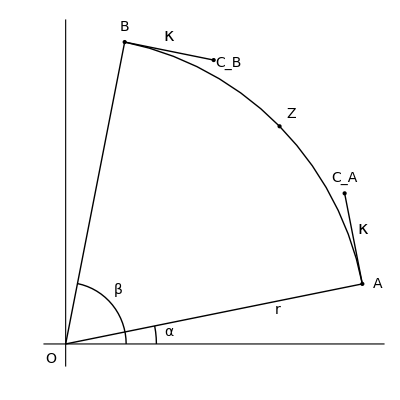

### Problem

#### Given:

Arc AB, with starting angle α, ending angle β.

#### Find:

A Bézier curve with endpoints A, B and control points C_A, C_B passing through the midpoint Z of AB.

### Solution

#### Let:

κ be the length of OverBar[AC_A].
We assume, by argument of symmetry, that the length κ of OverBar[AC_A] and OverBar[BC_B] are equal.
Since arc AB is tangent to OverBar[OA] and OverBar[OB], we require OverBar[AC_A] and OverBar[BC_B] to also be along the tangent; thus, (∠OAC)_A and (∠OBC)_B are right angles.

#### Calculations:

```mathematica
PointA={Cos[α],Sin[α]};
PointB={Cos[β],Sin[β]};
PointZ={Cos[(α+β)/2],Sin[(α+β)/2]};
```

```mathematica
PointCA=PointA+κ{Cos[α+π/2],Sin[α+π/2]}
```

{Cos[α]-κ Sin[α],κ Cos[α]+Sin[α]}

```mathematica
PointCB=PointB+κ{Cos[β-π/2],Sin[β-π/2]}
```

{Cos[β]+κ Sin[β],-κ Cos[β]+Sin[β]}

Parametric Bézier curve from A to B through C_A and C_B.

```mathematica
PBez[t_/;0≤t≤1]:=(1-t)^3 PointA+3(1-t)^2 t PointCA+3(1-t)t^2 PointCB+t^3 PointB
```

The midpoint on the Bézier curve is equal to the midpoint on arc AB:

```mathematica
κ=κ/.(Solve[PBez[1/2]==PointZ,κ]//Flatten)
```

(4 (Cos[α]+Cos[β]-2 Cos[(α+β)/2]))/(3 (Sin[α]-Sin[β]))

```mathematica
End[]
```

beziercontrol`

## Parametric equations for arcs.

```mathematica
Begin["paraarc`"]
```

paraarc`

Start angle α, end angle β.  Start point A={ax,ay}, end point B={bx,by}.
Assume center is O.

```mathematica
Tan[π/2-x]
```

Cot[x]

Equations for line OA, OB to find O:

Case 1: -π/4≤α≤π/4, -π/4≤β≤π/4

```mathematica
{x,y}/.Solve[{
(y-ay)==Tan[α](x-ax),
(y-by)==Tan[β](x-bx)},{x,y}]⟦1⟧
```

{-(ay-by-ax Tan[α]+bx Tan[β])/(Tan[α]-Tan[β]),-(-by Tan[α]+ay Tan[β]-ax Tan[α] Tan[β]+bx Tan[α] Tan[β])/(Tan[α]-Tan[β])}

Case 2: α<-π/4 or α>π/4, -π/4≤β≤π/4

```mathematica
{x,y}/.Solve[{
(x-ax)==Cot[α](y-ay),
(y-by)==Tan[β](x-bx)},{x,y}]⟦1⟧
```

{-(ax-ay Cot[α]+by Cot[α]-bx Cot[α] Tan[β])/(-1+Cot[α] Tan[β]),-(by+ax Tan[β]-bx Tan[β]-ay Cot[α] Tan[β])/(-1+Cot[α] Tan[β])}

Case 3:  -π/4≤α≤π/4, β<-π/4 or β>π/4

```mathematica
{x,y}/.Solve[{
(y-ay)==Tan[α](x-ax),
(x-bx)==Cot[β](y-by)},{x,y}]⟦1⟧
```

{-(bx+ay Cot[β]-by Cot[β]-ax Cot[β] Tan[α])/(-1+Cot[β] Tan[α]),-(ay-ax Tan[α]+bx Tan[α]-by Cot[β] Tan[α])/(-1+Cot[β] Tan[α])}

Case 4: α<-π/4 or α>π/4, β<-π/4 or β>π/4

```mathematica
{x,y}/.Solve[{
(x-ax)==Cot[α](y-ay),
(x-bx)==Cot[β](y-by)},{x,y}]⟦1⟧
```

{-(-bx Cot[α]+ax Cot[β]-ay Cot[α] Cot[β]+by Cot[α] Cot[β])/(Cot[α]-Cot[β]),-(ax-bx-ay Cot[α]+by Cot[β])/(Cot[α]-Cot[β])}

```mathematica
Origin[{ax,ay},{bx,by},α,β]
```

Origin[{ax,ay},{bx,by},α,β]

Radius r is distance from O to A (or B):

```mathematica
Origin[{ax,ay},{bx,by},α,β]
```

```mathematica
Radius[{ax_,ay_},{bx_,by_},α_,β_]:=With[
{o=Origin[{ax,ay},{bx,by},α,β]},
	√((ax-o⟦1⟧)^2+(bx-o⟦2⟧)^2)]
```

```mathematica
Radius[{ax,ay},{bx,by},α,β]
```

{0,√((ax-ay)^2+(bx-by)^2)}

Parametric equation:

```mathematica
Arc[{ax_,ay_},{bx_,by_},α_,β_,t:_/;0≤t≤1]:=With[
{o=Origin[{ax,ay},{bx,by},α,β],
r=Radius[{ax,ay},{bx,by},α,β],
γ=α+(β-α)t},
{o⟦1⟧+r Cos[γ],o⟦2⟧+r Sin[γ]}]
```

Midpoint is at t→1/2:

```mathematica
Arc[{ax,ay},{bx,by},α,β,1/2]
```

{{ax,ay+√((ax-ay)^2+(bx-by)^2) Cos[α+1/2 (-α+β)]},{bx,by+√((ax-ay)^2+(bx-by)^2) Sin[α+1/2 (-α+β)]}}

Degenerate case 1a: β → π/2

```mathematica
Origin[{ax,ay},{bx,by},α,π/2]
```

{bx,ay-ax Tan[α]+bx Tan[α]}

```mathematica
Radius[{ax,ay},{bx,by},α,π/2]
```

√((ax-bx)^2+(-ay+bx+ax Tan[α]-bx Tan[α])^2)

```mathematica
Arc[{ax,ay},{bx,by},α,π/2,1/2]
```

{bx+Cos[1/2 (π/2-α)+α] √((ax-bx)^2+(-ay+bx+ax Tan[α]-bx Tan[α])^2),ay-ax Tan[α]+bx Tan[α]+Sin[1/2 (π/2-α)+α] √((ax-bx)^2+(-ay+bx+ax Tan[α]-bx Tan[α])^2)}

Degenerate case 1b: β→(3π)/2:

```mathematica
Origin[{ax,ay},{bx,by},α,(3π)/2]
```

Solve::infc: The system -ay + y == (-ax + x)\ Tan[α] && -by + y == ComplexInfinity contains an infinite object ComplexInfinity.

ReplaceAll::reps: {-ay + y == (-ax + x)\ Tan[α], -by + y == ComplexInfinity} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.{-ay+y==(-ax+x) Tan[α],-by+y==ComplexInfinity}

Degenerate case 2: α→0, β→π/2:

```mathematica
Origin[{ax,ay},{bx,by},0,π/2]
```

{bx,ay}

```mathematica
Radius[{ax,ay},{bx,by},0,π/2]
```

√((ax-bx)^2+(-ay+bx)^2)

```mathematica
Arc[{ax,ay},{bx,by},0,π/2,1/2]
```

{bx+(√((ax-bx)^2+(-ay+bx)^2))/(√2),ay+(√((ax-bx)^2+(-ay+bx)^2))/(√2)}

```mathematica
End[]
```

paraarc`

## Finding the midpoint of an arc given its endpoints and angles.

A Bézier curve best approximates smaller arcs.  When the arc spans more than 90°, the approximation fails to match the arc.  Thus, we often need to split an arc into two smaller arcs.  Using our representation of the arc (endpoints and angles), this becomes a matter of finding the midpoint of the arc.

```mathematica
Begin["arcsplit`"]
```

arcsplit`

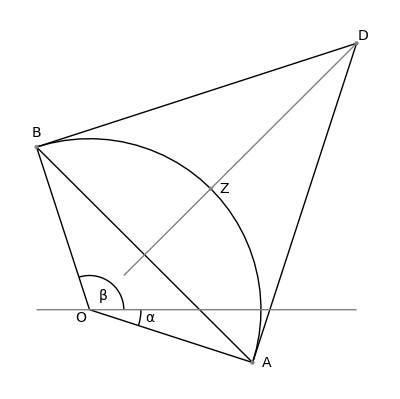

```mathematica
Show[Graphics[
Module[
{α=-(10π)/100,β=(60π)/100,a,b,d,z},
a={Cos[α],Sin[α]};
b={Cos[β],Sin[β]};
z={Cos[(α+β)/2],Sin[(α+β)/2]};
d={x,y}/.(Solve[{
y-a_⟦2⟧==Tan[α+π/2](x-a_⟦1⟧),
y-b_⟦2⟧==Tan[β-π/2](x-b_⟦1⟧)},{x,y}]//Flatten);
{
Circle[{0,0},1,{α,β}],
Circle[{0,0},0.3,{0,α}],
Circle[{0,0},0.2,{0,β}],
Line[{{0,0},a}],
Line[{{0,0},b}],
Line[{a,d}],
Line[{b,d}],
Line[{a,b}],
Text[Style["A",14], a+{0.08,0},Background->White],
Text[Style["B",14], b+{0,0.08},Background->White],
Text[Style["Z",14], z+{0.08,0},Background->White],
Text[Style["D",14], d+{0.04,0.04},Background->White],
Text[Style["O",14],{-0.05,-0.05},Background->White],
Text[Style["α",14],{0.35,-0.05},Background->White],
Text[Style["β",14],{0.08,0.08},Background->White],
RGBColor[0.5,0.5,0.5],
Line[{{0.2,0.2},d}],
Line[{{b_⟦1⟧,0},{d_⟦1⟧,0}}],
Thick,
PointSize[Large],
Point[{a,b,d,z},VertexColors->{Black,Black,Black,Black}]
}]
]]
```

### Problem

#### Given:

Arc AB, with starting angle α, ending angle β.

#### Find:

The midpoint Z of AB.

### Solution

#### Let:

OverBar[AD] and OverBar[BD] be tangents to arc AB intersecting at D; thus, ∠OAD and ∠OBD are right angles.

Point D can be found by solving the equations for OverBar[AB] and OverBar[BD:]

```mathematica
PointA={Cos[α],Sin[α]};PointB={Cos[β],Sin[β]};
```

```mathematica
PointD=Solve[{
y-PointA_⟦2⟧==Tan[α+π/2](x-PointA_⟦1⟧),
y-PointB_⟦2⟧==Tan[β-π/2](x-PointB_⟦1⟧)},{x,y}]⟦1⟧
```

{x→-(-Cos[α] Cot[α]+Cos[β] Cot[β]-Sin[α]+Sin[β])/(Cot[α]-Cot[β]),y→-(Cos[α] Cot[α] Cot[β]-Cos[β] Cot[α] Cot[β]+Cot[β] Sin[α]-Cot[α] Sin[β])/(Cot[α]-Cot[β])}

```mathematica
End[]
```

arcsplit`